```mathematica
experiments={
"EYrainbow_glucose",
"EYrainbow_glucose_largerBF",
"EYrainbow_rapamycin_1stTry",
"EYrainbow_rapamycin_CheckBistability",
"EYrainbow_1nmpp1_1st",
"EYrainbow_leucine_large",
"EYrainbowWhi5Up_betaEstrodiol"
};
data = Import[FileNameJoin[{NotebookDirectory[],"fitCellSizeWithOrganelle.csv"}],"Data","HeaderLines"->1];
epsilon = 10^(-18);
filled = data/.{0.->epsilon};
washed = Select[data,Function[x,NoneTrue[x,#==0&]]];
```

```mathematica
(* Check data *)
Position[filled,0.]
Position[washed,0.]
```

{}

{}

```mathematica
Length[filled]
Length[washed]
```

43108

29263

```mathematica
(* some fewer parameters *)
fitCellSizeFromOrganelles[dataset_,hasDiagonal_]:=Module[
{iEnd,jOffset,organelle,expr,a,b,c,alpha,beta,mean,mean0,n,n0,nu,sigma,nlm,params,fittedFunc,fitted,fittedMin,fittedMax,dataMin,dataMax},
(*organelle=Table[
(n[i]-n0[i])(mean[i]-mean0[i]),
{i,1,6}
];*)
organelle = {
n[1]-n0[1],
mean[2]-mean0[2],
mean[3]-mean0[3],
n[4]-n0[4],
(n[5]-n0[5])(mean[5]-mean0[5]),
n[6]-n0[6]
};
iEnd=If[hasDiagonal,6,5];
jOffset = If[hasDiagonal,0,1];
expr = Sum[a[i]organelle[[i]],{i,1,6}]+Sum[organelle[[i]] b[i,j]organelle[[j]],{i,1,iEnd},{j,i+jOffset,6}]+c;
nlm = NonlinearModelFit[
dataset[[All,2;;]],
expr,
Join[
Table[a[i],{i,1,6}],
Flatten[Table[b[i,j],{i,1,iEnd},{j,i+jOffset,6}]],
{c},
Table[n0[i],{i,1,6}],
Table[mean0[i],{i,1,6}]
],
Join[
Table[mean[i],{i,1,6}],
Table[n[i],{i,1,6}]
],
MaxIterations->∞
];
params=nlm["BestFitParameters"];
Print["CellSize = Sum[a[i]*organalle[i]]+Sum[organelle[i]*b[i,j]*organelle[j]]+c"];
Print["a[i]: ",Table[a[i],{i,1,6}]/.params];
Print["b[i,j]: ",Table[b[i,j],{i,1,6},{j,1,6}]/.params//MatrixForm];
Print["c: ", c/.params];
Print["organalle = (n-n0)(mean-mean0)"];
Print["n0[i]: ",Table[n0[i],{i,1,6}]/.params];
Print["mean0[i]: ",Table[mean0[i],{i,1,6}]/.params];
Print["Adjusted R Square: ", nlm["AdjustedRSquared"]];
Print["p-values for parameter z-statistics: ", nlm["ParameterPValues"]];
Print["t-statistics for parameter estimates: ", nlm["ParameterTStatistics"]];
fittedFunc = Function[
vec,
expr/.params
/.Table[n[i]->vec[[i]],{i,1,6}]
/.Table[mean[i]->vec[[i+6]],{i,1,6}]
];
fitted = Map[fittedFunc,dataset[[All,2;;-2]]];
fittedMin = Min[fitted];
fittedMax = Max[fitted];
dataMin = Min[dataset[[All,-1]]];
dataMax = Max[dataset[[All,-1]]];
Print[Show[
ListPlot[
Transpose[{dataset[[All,-1]],fitted}],
PlotTheme->"Scientific",AspectRatio->(fittedMax)/(dataMax)
],
Plot[x,{x,0,dataMax}]
]];
Print[""]
]
```

All Experiments, Null Organelles filled with 0:

CellSize = Sum[a[i]*organalle[i]]+Sum[organelle[i]*b[i,j]*organelle[j]]+c

a[i]: {20.9599,7.21565,38.0078,-0.692013,-6.13636,-38.1178}

b[i,j]: (b$5101[1,1] | 0.0209382 | 0.0706873 | -0.0464541 | 0.0225159 | -0.120722
b$5101[2,1] | b$5101[2,2] | -0.000142699 | -0.00567983 | 0.000305728 | -0.0100549
b$5101[3,1] | b$5101[3,2] | b$5101[3,3] | 0.0830913 | -0.00704661 | -0.02189
b$5101[4,1] | b$5101[4,2] | b$5101[4,3] | b$5101[4,4] | -0.00163808 | -0.061947
b$5101[5,1] | b$5101[5,2] | b$5101[5,3] | b$5101[5,4] | b$5101[5,5] | 0.050018
b$5101[6,1] | b$5101[6,2] | b$5101[6,3] | b$5101[6,4] | b$5101[6,5] | b$5101[6,6])

c: 6451.24

organalle = (n-n0)(mean-mean0)

n0[i]: {225.331,1.,1.,158.425,0.196247,-229.082}

mean0[i]: {1.,61.9105,-43.3313,1.,-3.49464,1.}

Adjusted R Square: 0.930993

p-values for parameter z-statistics: {1.23684×10^-55,2.31909×10^-193,7.77226×10^-106,0.684652,4.39552×10^-12,2.29904×10^-233,5.98895×10^-88,4.86505×10^-26,3.21395×10^-7,5.10239×10^-13,4.72541×10^-71,0.733129,3.5367×10^-11,0.186449,8.83092×10^-170,6.40681×10^-99,5.14045×10^-8,1.64212×10^-13,0.51517,5.63966×10^-45,0.,0.,0.,0.,0.,0.,2.15396×10^-17,0.,0.,0.,1.92491×10^-14,0.,2.81925×10^-219,0.}

t-statistics for parameter estimates: {15.7354,29.8151,21.9108,-0.406126,-6.92581,-32.8204,19.9264,10.5609,-5.11125,7.22477,-17.8555,-0.340969,-6.62402,1.32118,-27.8994,21.1651,-5.44735,-7.37748,-0.650815,-14.0883,45.4715,44558.8,74.7253,∞,∞,638.442,8.48877,-40.4447,∞,57.9307,-7.6582,∞,-31.7929,∞}

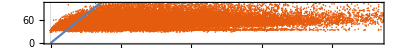

```mathematica
Print["All Experiments, Null Organelles filled with 0:"];
fitCellSizeFromOrganelles[filled,False];
```

```mathematica
Print["All Experiments, Null Organelles Excluded:"];
fitCellSizeFromOrganelles[washed,False];
```

```mathematica
Do[
Print[experiments[[i]],", Null Organelles filled with 0:"];
fitCellSizeFromOrganelles[Select[filled,#[[1]]==experiments[[i]]&]];,
{i,1,Length[experiments]}
];
Do[
Print[experiments[[i]],", Null Organelles Excluded:"];
fitCellSizeFromOrganelles[Select[washed,#[[1]]==experiments[[i]]&]];,
{i,1,Length[experiments]}
];
```